```mathematica
i = {0, 5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 52, 54, 56, 68};
u = {-69, -65, -58, -49, -38, -23, -5, 23, 62, 128, 306, 762, 1664, 1621, 1620};
```

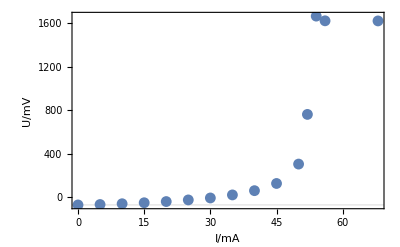

```mathematica
ListPlot[Transpose[{i, u}], Frame->True, FrameLabel->{"I/mA", "U/mV"}, GridLines->{{}, {-69}}]
```

```mathematica
x = {0, 0.3, 0.6, 1, 1.3, 2, 2.3, 2.6, 3.3, 4, 5};
u2 = {749, 257, 218, 55, 3, -28, -44, -52, -63, -68, -69};
```

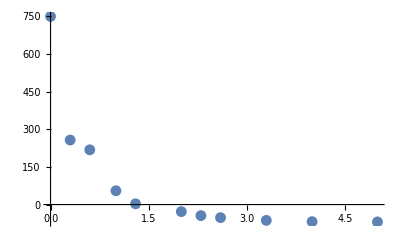

```mathematica
ListPlot[Transpose[{x, u2}]]
```

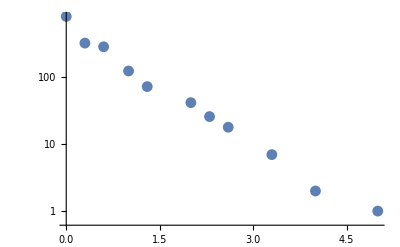

```mathematica
ListLogPlot[Transpose[{x, u2+70}]]
```

```mathematica
xmess = -Log[10, (u2+70)/(749+70)] // N
```

{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801,2.06819,2.61225,2.91328}

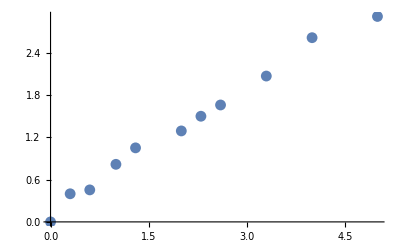

```mathematica
ListPlot[Transpose[{x, xmess}]]
```

```mathematica
tab=Transpose[{x,100*10^-x//N,u2}];
tab//TableForm
```

0 | 100. | 749
0.3 | 50.1187 | 257
0.6 | 25.1189 | 218
1 | 10. | 55
1.3 | 5.01187 | 3
2 | 1. | -28
2.3 | 0.501187 | -44
2.6 | 0.251189 | -52
3.3 | 0.0501187 | -63
4 | 0.01 | -68
5 | 0.001 | -69

```mathematica
Export["/home/moritz/FP2/0407-Optisches Pumpen/data/part5/04.10/filters.txt",tab,"Table"]
```

/home/moritz/FP2/0407-Optisches Pumpen/data/part5/04.10/filters.txt